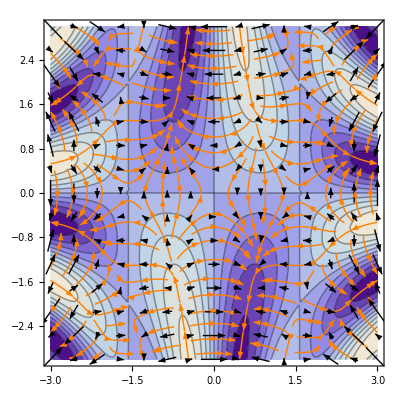

```mathematica
ClearAll["Global`*"]
(* ColorFunction->"LakeColors" is the Mathematica default *)
min=-3;
max=3;

(*surf[x_,y_]:=Sin[x]Sin[y];*)
surf[x_,y_]:=Sin[x y]Cos[x];
u[x_,y_] = - D[surf[x,y],x];
v[x_,y_] = - D[surf[x,y],y];


dp=DensityPlot[Sqrt[u[x,y]^2+v[x,y]^2],{x,min,max},{y,min,max}];
cp=ContourPlot[surf[x,y],{x,min,max},{y,min,max},ColorFunction->"LakeColors"];
vp =VectorPlot[{u[x,y],v[x,y]},{x,min,max},{y,min,max},VectorStyle->{Black}];
sp = StreamPlot[{u[x,y],v[x,y]},{x,min,max},{y,min,max},StreamStyle->Orange];
(*StreamDensityPlot[{vx[x,y],vy[x,y]},{x,min,max},{y,min,max}]*)(*VectorDensityPlot[{vx[x,y],vy[x,y]},{x,min,max},{y,min,max}]*)
(*GraphicsGrid[{{cp,dp},{vp,sp}}]*)


Show[cp,sp,vp]
```

```mathematica
(*colorfunction1=ColorData["LakeColors"]
OwnValues[colorfunction1]*)
```

```mathematica
(*Eigenvalues[{{a,b},{c,d}}]*)
```

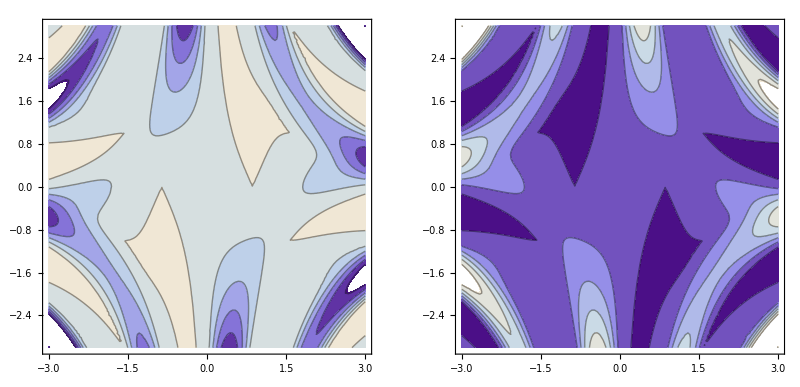

```mathematica
dudx[x_,y_]=D[u[x,y],x];
dudy[x_,y_]=D[u[x,y],y];
dvdx[x_,y_]=D[v[x,y],x];
dvdy[x_,y_]=D[v[x,y],y];
eigen1[x_,y_]=Eigenvalues[{{dudx[x,y],dudy[x,y]},{dvdx[x,y],dvdy[x,y]}}][[1]];
eigen2[x_,y_]=Eigenvalues[{{dudx[x,y],dudy[x,y]},{dvdx[x,y],dvdy[x,y]}}][[2]];
 
e1p=ContourPlot[eigen1[x,y],{x,min,max},{y,min,max}];
e2p=ContourPlot[eigen2[x,y],{x,min,max},{y,min,max}];
GraphicsGrid[{{e1p,e2p}}]
```

```mathematica
(*
ncfile="/Volumes/Workspace/tkleiner/data/Paper/paper_BIS_RLIS/data/nc/sl30ka_2500m_mean10ka.nc";
vx=Import[ncfile,{"Datasets","u"}];
vy=Import[ncfile,{"Datasets","v"}];
*)
```